# Electrostatic potential for a charge near metal electrode covered with dielectric

## Units

```mathematica
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

## Parameters

Dielectric permittivities:
solvent: ϵ_s
SAM: ϵ_m

Geometry:
R - Radius of a shperical cavity around the charge
d - distance from the charge to the electrode surface.

```mathematica
ϵs=78;
```

```mathematica
ϵinf=3.78;
```

```mathematica
τD=8.3;
```

## Analytical integration

```mathematica
Integrate[Exp[-2R t]/(1+κ Exp[-2(d-R)t]),{t,0,∞},Assumptions->{R>0,d>0,d>R,κ<0}]
```

If[κ<-1,1/(2 (d-2 R) R)ⅇ^((ⅈ d π)/(d-R)) κ^(-(d+R)/(d-R)) ((d-2 R) (-κ)^(d/(d-R)) Gamma[d/(d-R)] Gamma[(d-2 R)/(d-R)]+R (-κ)^((2 R)/(d-R)) Hypergeometric2F1[1,(d-2 R)/(d-R),(2 d-3 R)/(d-R),-1/κ] (Cos[(π R)/(d-R)]+ⅈ Sin[(π R)/(d-R)])),1/2 ((κ^(-R/(d-R)) Gamma[d/(d-R)] Gamma[(d-2 R)/(d-R)])/R+(ⅈ ⅇ^(-(ⅈ π R)/(d-R)) π Hypergeometric2F1[1,R/(d-R),d/(d-R),-κ])/(R Gamma[(d-2 R)/(d-R)] Gamma[R/(d-R)])+(ⅇ^((ⅈ π (d-2 R))/(d-R)) Cos[(π R)/(d-R)] Hypergeometric2F1[1,2+d/(-d+R),3+d/(-d+R),-1/κ])/(d κ-2 R κ))]

## Polarization induced potentials

```mathematica
Φ[R_,d_,ϵs_,ϵm_,Q_]:=Module[{κ,integral1,integral2},
κ=(ϵm-ϵs)/(ϵm+ϵs);
integral1=Integrate[Exp[-2R t]/(1+κ Exp[-2(d-R)t]),{t,0,∞}];
integral2=Integrate[Exp[-2d t]/(1+κ Exp[-2(d-R)t]),{t,0,∞}];
-Q/ϵs(κ integral1+integral2)+Q/R(1/ϵs-1)];
```

```mathematica
N[Φ[10,10,80,80,1]]
```

-0.099375

```mathematica
N[Φ[10,15,80,80,1]]
```

-0.0991667

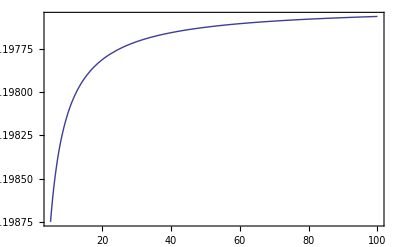

```mathematica
Plot[N[Φ[5,x,80,80,1]],{x,5,100},Axes->False,Frame->True,PlotRange->All]
```

## Spectral Density (Tanaka-Hsu)

Debye dielectric function:

```mathematica
ϵD[ω_,ϵs_,ϵinf_,τ_]:=ϵinf+(ϵs-ϵinf)/(1-ⅈ ω cm2au τD ps2au);
```

Frequency dependent potential (Tanaka-Hsu):

```mathematica
Φ0[R_,d_,ϵs_,ϵinf_,τ_,ω_]:=Module[{f1,f2},
f1=-1/(2 d)1/ϵD[ω,ϵs,ϵinf,τ];
f2=1/R(1/ϵD[ω,ϵs,ϵinf,τ]-1);
f1+f2];
```

Spectral density (Tanaka-Hsu):

```mathematica
J0[R_,d_,ϵs_,ϵinf_,τ_,Q_,ω_]:=-Q^2/2 Im[Φ0[R,d,ϵs,ϵinf,τ,ω]];
```

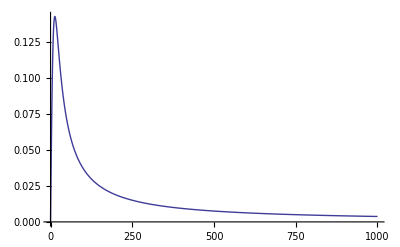

```mathematica
Plot[au2ev J0[10,30,ϵs,ϵinf,τ,1.0,ω],{ω,0,1000},PlotRange->All]
```

```mathematica
NIntegrate[au2kcal 2/π J0[10,30,ϵs,ϵinf,τD,1.0,ω]/ω,{ω,0,∞}]
```

6.58178+0. ⅈ